```mathematica
s=.7;
sp=.5;
α=.8;
ϕ=1;
β=π/6;
x=(1-(ϕ+α sp)t)/(α sp/s);
y=(1-(ϕ-α sp)t)/(α sp/s);q1=(1-x y+√(1-x^2)√(1-y^2))/2;q2=(1-x y-√(1-x^2)√(1-y^2))/2;
{(1-α sp/s)/(ϕ-α sp),1/ϕ}
out=Show[ParametricPlot[{q1,q2},{t,(1-α sp/s)/(ϕ-α  sp),1/ϕ},PlotRange->{{-0.1,1.1},{-.1,1.1}}],ParametricPlot[{q2,q1},{t,(1-α sp/s)/(ϕ-α sp),1/ϕ},PlotRange->{{-0.1,1.1},{-.1,1.1}}],Graphics[Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}]],Graphics[{Dashed,Line[{{0,0},{1,1}}]}]
];

x=(1-(ϕ-α sp)t)/(-α sp/s);
y=(1-(ϕ+α sp)t)/(-α sp/s);q1=(1-x y+√(1-x^2)√(1-y^2))/2;q2=(1-x y-√(1-x^2)√(1-y^2))/2;
{1/ϕ,(1+α sp/s)/(ϕ-α sp)}

in=Show[ParametricPlot[{q1,q2},{t,1/ϕ,(1+α sp/s)/(ϕ-α sp)},PlotRange->{{-0.1,1.1},{-.1,1.1}},PlotStyle-> Red],ParametricPlot[{q2,q1},{t,1/ϕ,(1+α sp/s)/(ϕ-α sp)},PlotRange->{{-0.1,1.1},{-.1,1.1}},PlotStyle-> Red]];
SUS={t->1/(2 (sp α-ϕ) (sp α+ϕ))Csc[β] Sec[β] (-2 s ϕ √(Cos[β] Sin[β])+sp^2 α^2 (Cos[β]+Sin[β])-sp α √(sp^2 α^2-4 s ϕ √(Cos[β] Sin[β]) (Cos[β]+Sin[β])+(2 s^2-sp^2 α^2+2 ϕ^2) Sin[2 β])),t->1/(2 (sp α-ϕ) (sp α+ϕ))(-2 s ϕ √(Csc[β] Sec[β])+sp α Csc[β] Sec[β] (sp α (Cos[β]+Sin[β])+√(sp^2 α^2-4 s ϕ √(Cos[β] Sin[β]) (Cos[β]+Sin[β])+(2 s^2-sp^2 α^2+2 ϕ^2) Sin[2 β])))};

Clear[t]
ppp1=Graphics[{Black,PointSize->Medium,Point[{Cos[β]t,Sin[β]t}/. SUS[[1]]]}];
ppp2=Graphics[{Black,PointSize->Medium,Point[{Cos[β]t,Sin[β]t}/. SUS[[2]]]}];
lll=ParametricPlot[{Cos[β]t,Sin[β]t},{t,0,Max[t/. SUS[[1]],t/. SUS[[2]]]}];
asy=ParametricPlot[{√(Cos[β]/Sin[β])s,√(Sin[β]/Cos[β])s},{β,.45,π/2-.45},PlotStyle-> Dashed];


SA1=Show[in,out,ppp1,ppp2,lll,asy]
```

{0.714286,1}

{1,2.61905}

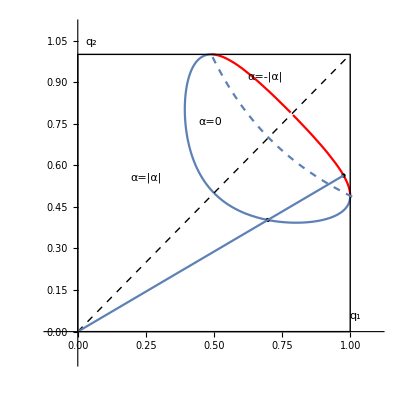

```mathematica
Show[in,out,asy]
```

```mathematica
Clear[s,sp,α,ϕ]
```

```mathematica
ϕ=1;α=1;

x=(1-(ϕ+α sp)t)/(α sp/s);
y=(1-(ϕ-α sp)t)/(α sp/s);q1=(1-x y+√((1-x^2)(1-y^2)))/2;q2=(1-x y-√((1-x^2)(1-y^2)))/2
```

1/2 (1-(s^2 (1-(1-sp) t) (1-(1+sp) t))/sp^2-√((1-(s^2 (1-(1-sp) t)^2)/sp^2) (1-(s^2 (1-(1+sp) t)^2)/sp^2)))

```mathematica
xx=x/. t->(1-sp^2/s^2)/(1-sp^2)//FullSimplify
yy=y/. t->(1-sp^2/s^2)/(1-sp^2)//FullSimplify
```

(s^2-sp)/(s (-1+sp))

(s^2+sp)/(s+s sp)

```mathematica
qq1=FullSimplify[q1 /.t->(1-sp^2/s^2)/(1-sp^2)//FullSimplify,{0<s<1,0<sp<s}]
qq2=FullSimplify[q2 /.t->(1-sp^2/s^2)/(1-sp^2)//FullSimplify,{0<s<1,0<sp<s}]
```

(-s^2+sp^2)/(s^2 (-1+sp^2))

(-s^2+sp^2)/(-1+sp^2)

```mathematica
FullSimplify[((√(qq2(1-qq2)))/(sp/s)((√(1-yy^2)(1+sp)-√(1-xx^2)(1-sp))/(√((1-xx^2)(1-yy^2)))))//FullSimplify,{0<s<1,0<sp<s}]
```

0

```mathematica
FullSimplify[((√(qq1(1-qq1)))/(sp/s)((√(1-yy^2)(1+sp)+√(1-xx^2)(1-sp))/(√((1-xx^2)(1-yy^2)))))//FullSimplify,{0<s<1,0<sp<s}]
```

2

```mathematica
Limit[(√(qq1(1-qq1)))/(sp/s)((√(1-yy^2)(1+sp)+√(1-xx^2)(1-sp))/(√((1-xx^2)(1-yy^2)))), sp->0]//FullSimplify
```

-(2 √(1/s^2) s (-1+s^2))/(√((-1+s^2)^2))

```mathematica
qq1/. sp->0
qq2/. sp->0
```

1

s^2

## New

{0.666667,1}

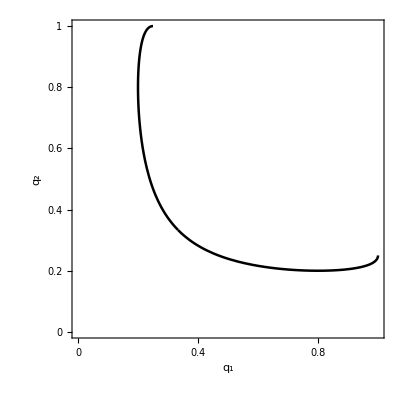

{1,2.}

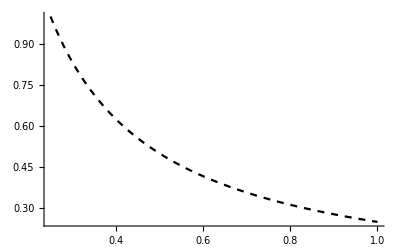

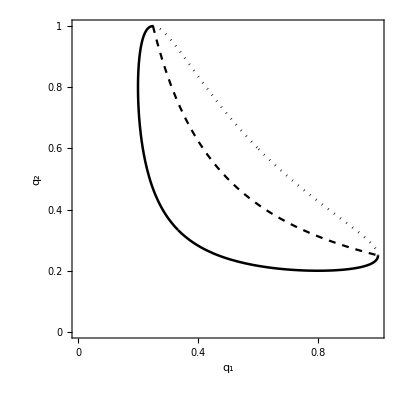

```mathematica
s=0.5;
sp=s^2;
α=1;
ϕ=1;
β=π/6;
x=(1-(ϕ+α sp)t)/(α sp/s);
y=(1-(ϕ-α sp)t)/(α sp/s);q1=(1-x y+√(1-x^2)√(1-y^2))/2;q2=(1-x y-√(1-x^2)√(1-y^2))/2;
{(1-α sp/s)/(ϕ-α sp),1/ϕ}
out=Show[
ParametricPlot[{q1,q2},{t,(1-α sp/s)/(ϕ-α  sp),1/ϕ},PlotRange->{{0,1},{0,1}}
,AspectRatio-> 1,PlotStyle->Directive[Thickness[.0045],Black],FrameTicks->{{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}},{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}}},FrameTicksStyle->{{Black,Black},{Black,Black}},
Frame->True,FrameLabel->{Subscript[q, 1],Subscript[q, 2]},FrameStyle->Directive[Black,FontSize->18,FontFamily->"Times"]
],
ParametricPlot[{q2,q1},{t,(1-α sp/s)/(ϕ-α sp),1/ϕ},PlotRange->{{0,1},{0,1}},AspectRatio-> 1,PlotStyle->Directive[Thickness[.0045],Black],FrameTicks->{{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}},{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}}},FrameTicksStyle->{{Black,Black},{Black,Black}},
Frame->True,FrameLabel->{Subscript[q, 1],Subscript[q, 2]},FrameStyle->Directive[Black,FontSize->18,FontFamily->"Times"]
]
]

x=(1-(ϕ-α sp)t)/(-α sp/s);
y=(1-(ϕ+α sp)t)/(-α sp/s);q1=(1-x y+√(1-x^2)√(1-y^2))/2;q2=(1-x y-√(1-x^2)√(1-y^2))/2;
{1/ϕ,(1+α sp/s)/(ϕ-α sp)}

in=Show[ParametricPlot[{q1,q2},{t,1/ϕ,(1+α sp/s)/(ϕ-α sp)},PlotRange->{{0,1},{0,1}},AspectRatio-> 1,PlotStyle->Directive[Thickness[.0045],Black,Dotted],FrameTicks->{{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}},{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}}},FrameTicksStyle->{{Black,Black},{Black,Black}},
Frame->True,FrameLabel->{Subscript[q, 1],Subscript[q, 2]},FrameStyle->Directive[Black,FontSize->18,FontFamily->"Times"]
],
ParametricPlot[{q2,q1},{t,1/ϕ,(1+α sp/s)/(ϕ-α sp)},PlotRange->{{0,1},{0,1}},AspectRatio-> 1,PlotStyle->Directive[Thickness[.0045],Black,Dotted],FrameTicks->{{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}},{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}}},FrameTicksStyle->{{Black,Black},{Black,Black}},
Frame->True,FrameLabel->{Subscript[q, 1],Subscript[q, 2]},FrameStyle->Directive[Black,FontSize->18,FontFamily->"Times"]]];
SUS={t->1/(2 (sp α-ϕ) (sp α+ϕ))Csc[β] Sec[β] (-2 s ϕ √(Cos[β] Sin[β])+sp^2 α^2 (Cos[β]+Sin[β])-sp α √(sp^2 α^2-4 s ϕ √(Cos[β] Sin[β]) (Cos[β]+Sin[β])+(2 s^2-sp^2 α^2+2 ϕ^2) Sin[2 β])),t->1/(2 (sp α-ϕ) (sp α+ϕ))(-2 s ϕ √(Csc[β] Sec[β])+sp α Csc[β] Sec[β] (sp α (Cos[β]+Sin[β])+√(sp^2 α^2-4 s ϕ √(Cos[β] Sin[β]) (Cos[β]+Sin[β])+(2 s^2-sp^2 α^2+2 ϕ^2) Sin[2 β])))};

Clear[t]
ppp1=Graphics[{Black,PointSize->Medium,Point[{Cos[β]t,Sin[β]t}/. SUS[[1]]]}];
ppp2=Graphics[{Black,PointSize->Medium,Point[{Cos[β]t,Sin[β]t}/. SUS[[2]]]}];
lll=ParametricPlot[{Cos[β]t,Sin[β]t},{t,0,Max[t/. SUS[[1]],t/. SUS[[2]]]}];
asy=Plot[s^2/(ϕ^2 q1),{q1,s^2/ϕ^2,1},PlotStyle->Directive[Thickness[.004],Black,Dashed]]


SA1=Show[in,out,asy]
```

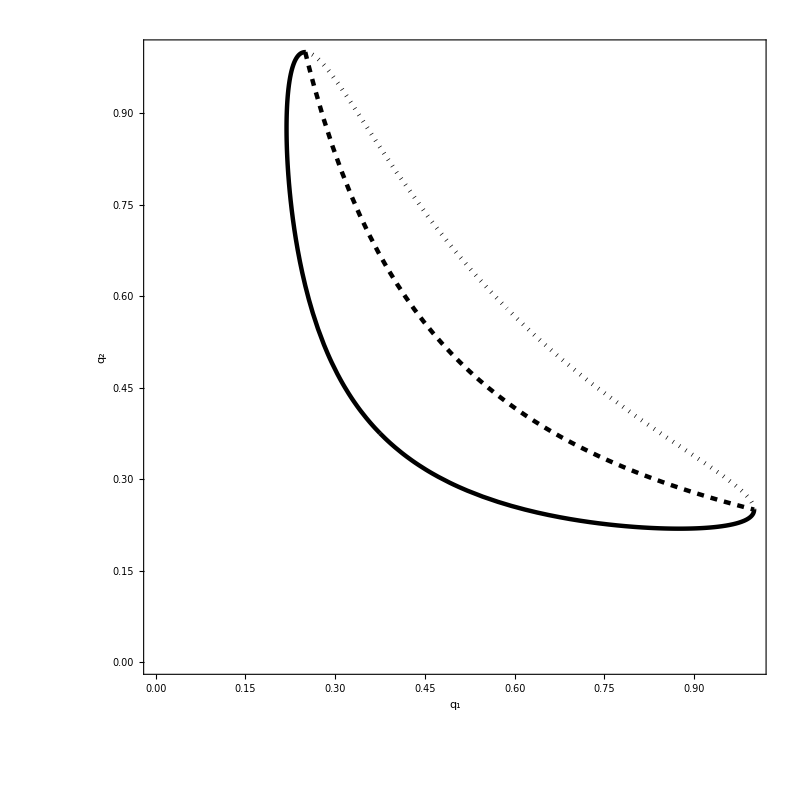

## New 2

{(1-0.5 α)/(1-0.25 α),1}

Power::infy: Infinite expression 1/0.^2 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 1 + ComplexInfinity + ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

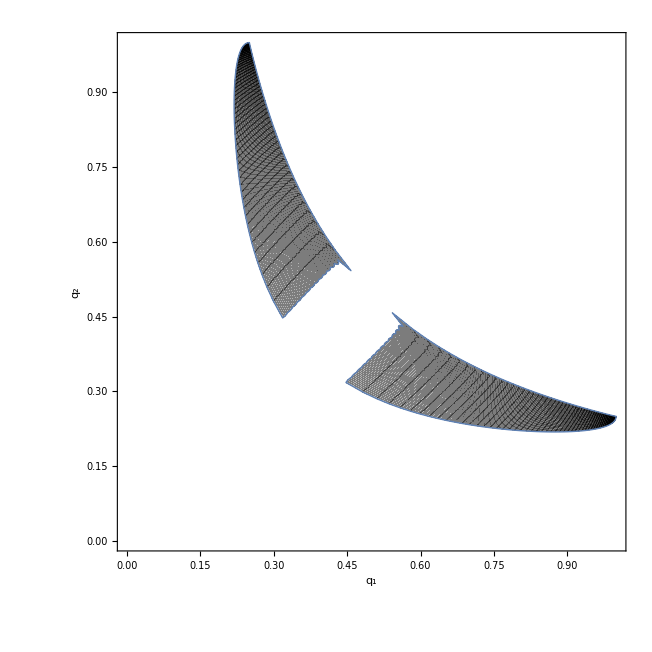

{1,(1+0.5 α)/(1-0.25 α)}

ParametricPlot::plln: Limiting value 1 + 0.5\ α/1 - 0.25\ α in {t, 1/ϕ, 1 + α\ sp/s/ϕ - α\ sp} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[ParametricPlot[{q1, q2}, {t, 1/ϕ, 1 + α\ (sp\ Power[« 2 »])/ϕ - Times[« 2 »]}, PlotRange → {{0, 1}, {0, 1}}, PlotStyle → Directive[Thickness[0.004], Black, Dotted], Frame → True, FrameLabel → {q_1, q_2}, FrameStyle → Directive[Black, FontSize → 11, FontFamily → "Times"]], ParametricPlot[{q2, q1}, {t, 1/ϕ, 1 + α\ (sp\ Power[« 2 »])/ϕ - Times[« 2 »]}, « 3 », FrameLabel → {q_1, q_2}, FrameStyle → Directive[Black, FontSize → 11, FontFamily → "Times"]]].

ParametricPlot::plln: Limiting value 1 + 0.5\ α/1 - 0.25\ α in {t, 1/ϕ, 1 + α\ sp/s/ϕ - α\ sp} is not a machine-sized real number.

General::stop: Further output of ParametricPlot :: plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ParametricPlot[{q1, q2}, {t, 1/ϕ, 1 + α\ (sp\ Power[« 2 »])/ϕ - Times[« 2 »]}, PlotRange → {{0, 1}, {0, 1}}, PlotStyle → Directive[Thickness[0.004], Black, Dotted], Frame → True, FrameLabel → {q_1, q_2}, FrameStyle → Directive[Black, FontSize → 11, FontFamily → "Times"]], ParametricPlot[{q2, q1}, {t, 1/ϕ, 1 + α\ (sp\ Power[« 2 »])/ϕ - Times[« 2 »]}, « 3 », FrameLabel → {q_1, q_2}, FrameStyle → Directive[Black, FontSize → 11, FontFamily → "Times"]]].

ParametricPlot::plln: Limiting value Max[2\ (-0.658037 + 0.0853766\ α^2 - 0.25\ α\ √-1.79779 + 0.0625\ Power[« 2 »] + 1/2\ Power[« 2 »]\ Plus[« 2 »])/√3\ (-1 + 0.25\ α)\ (1 + 0.25\ α), -1.51967 + 0.57735\ α\ (0.341506\ α + √-1.79779 + Times[« 2 »] + Times[« 3 »])/2\ (-1 + 0.25\ α)\ (1 + 0.25\ α)] in {t, 0, Max[t/. SUS ⟦ 1 ⟧, t/. SUS ⟦ 2 ⟧]} is not a machine-sized real number.

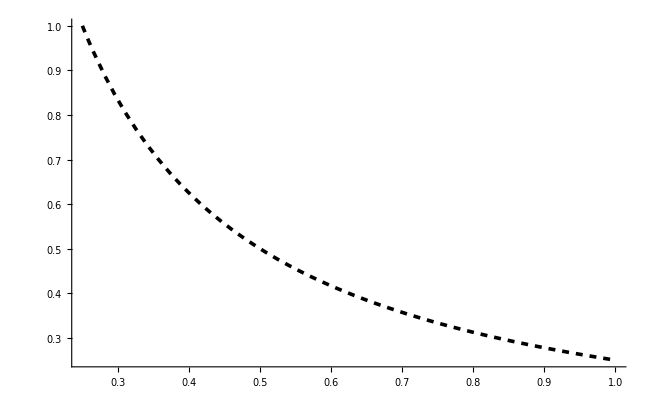

ParametricPlot::plln: Limiting value 1 + 0.5\ α/1 - 0.25\ α in {t, 1/ϕ, 1 + α\ sp/s/ϕ - α\ sp} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[ParametricPlot[{q1, q2}, {t, 1/ϕ, 1 + α\ (sp\ Power[« 2 »])/ϕ - Times[« 2 »]}, PlotRange → {{0, 1}, {0, 1}}, PlotStyle → Directive[Thickness[0.004], Black, Dotted], Frame → True, FrameLabel → {q_1, q_2}, FrameStyle → Directive[Black, FontSize → 11, FontFamily → "Times"]], ParametricPlot[{q2, q1}, {t, 1/ϕ, 1 + α\ (sp\ Power[« 2 »])/ϕ - Times[« 2 »]}, « 3 », FrameLabel → {q_1, q_2}, FrameStyle → Directive[Black, FontSize → 11, FontFamily → "Times"]]].

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value 1 + 0.5\ α/1 - 0.25\ α in {t, 1/ϕ, 1 + α\ sp/s/ϕ - α\ sp} is not a machine-sized real number.

General::stop: Further output of ParametricPlot :: plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ParametricPlot[{q1, q2}, {t, 1/ϕ, 1 + α\ (sp\ Power[« 2 »])/ϕ - Times[« 2 »]}, PlotRange → {{0, 1}, {0, 1}}, PlotStyle → Directive[Thickness[0.004], Black, Dotted], Frame → True, FrameLabel → {q_1, q_2}, FrameStyle → Directive[Black, FontSize → 11, FontFamily → "Times"]], ParametricPlot[{q2, q1}, {t, 1/ϕ, 1 + α\ (sp\ Power[« 2 »])/ϕ - Times[« 2 »]}, « 3 », FrameLabel → {q_1, q_2}, FrameStyle → Directive[Black, FontSize → 11, FontFamily → "Times"]]].

General::stop: Further output of Show :: gcomb will be suppressed during this calculation.

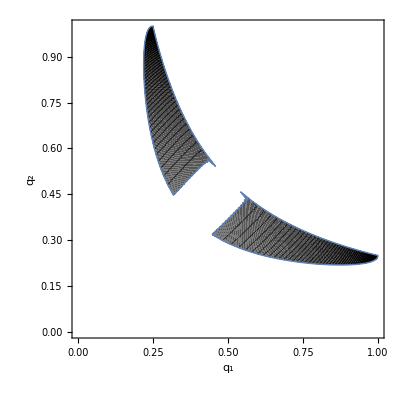
Show[Show[ParametricPlot[{q1,q2},{t,1/ϕ,(1+(α sp)/s)/(ϕ-α sp)},PlotRange→{{0,1},{0,1}},PlotStyle→Directive[Thickness[0.004],Black,Dotted],Frame→True,FrameLabel→{q_1,q_2},FrameStyle→Directive[Black,FontSize→11,FontFamily→Times]],ParametricPlot[{q2,q1},{t,1/ϕ,(1+(α sp)/s)/(ϕ-α sp)},PlotRange→{{0,1},{0,1}},PlotStyle→Directive[Thickness[0.004],Black,Dotted],Frame→True,FrameLabel→{q_1,q_2},FrameStyle→Directive[Black,FontSize→11,FontFamily→Times]]],-Graphics-,-Graphics-]

```mathematica
s=.5;
sp=s^2;
(*α=.8;*)
ϕ=1;
β=π/6;
x=(1-(ϕ+α sp)t)/(α sp/s);
y=(1-(ϕ-α sp)t)/(α sp/s);q1=(1-x y+√(1-x^2)√(1-y^2))/2;q2=(1-x y-√(1-x^2)√(1-y^2))/2;
{(1-α sp/s)/(ϕ-α sp),1/ϕ}
out=Show[
ParametricPlot[{q1,q2},{α,0,.8},{t,(1-α sp/s)/(ϕ-α  sp),1/ϕ},PlotRange->{{0,1},{0,1}},
PlotStyle->Directive[Thickness[.004],Black],
Frame->True,FrameLabel->{Subscript[q, 1],Subscript[q, 2]},FrameStyle->Directive[Black,FontSize->11,FontFamily->"Times"]
],
ParametricPlot[{q2,q1},{α,0,.8},{t,(1-α sp/s)/(ϕ-α sp),1/ϕ},PlotRange->{{0,1},{0,1}},
PlotStyle->Directive[Thickness[.004],Black],
Frame->True,FrameLabel->{Subscript[q, 1],Subscript[q, 2]},FrameStyle->Directive[Black,FontSize->11,FontFamily->"Times"]
]
]

x=(1-(ϕ-α sp)t)/(-α sp/s);
y=(1-(ϕ+α sp)t)/(-α sp/s);q1=(1-x y+√(1-x^2)√(1-y^2))/2;q2=(1-x y-√(1-x^2)√(1-y^2))/2;
{1/ϕ,(1+α sp/s)/(ϕ-α sp)}

in=Show[ParametricPlot[{q1,q2},{t,1/ϕ,(1+α sp/s)/(ϕ-α sp)},PlotRange->{{0,1},{0,1}},
PlotStyle->Directive[Thickness[.004],Black,Dotted],
Frame->True,FrameLabel->{Subscript[q, 1],Subscript[q, 2]},FrameStyle->Directive[Black,FontSize->11,FontFamily->"Times"]
],
ParametricPlot[{q2,q1},{t,1/ϕ,(1+α sp/s)/(ϕ-α sp)},PlotRange->{{0,1},{0,1}},PlotStyle->Directive[Thickness[.004],Black,Dotted],
Frame->True,FrameLabel->{Subscript[q, 1],Subscript[q, 2]},FrameStyle->Directive[Black,FontSize->11,FontFamily->"Times"]]];
SUS={t->1/(2 (sp α-ϕ) (sp α+ϕ))Csc[β] Sec[β] (-2 s ϕ √(Cos[β] Sin[β])+sp^2 α^2 (Cos[β]+Sin[β])-sp α √(sp^2 α^2-4 s ϕ √(Cos[β] Sin[β]) (Cos[β]+Sin[β])+(2 s^2-sp^2 α^2+2 ϕ^2) Sin[2 β])),t->1/(2 (sp α-ϕ) (sp α+ϕ))(-2 s ϕ √(Csc[β] Sec[β])+sp α Csc[β] Sec[β] (sp α (Cos[β]+Sin[β])+√(sp^2 α^2-4 s ϕ √(Cos[β] Sin[β]) (Cos[β]+Sin[β])+(2 s^2-sp^2 α^2+2 ϕ^2) Sin[2 β])))};

Clear[t]
ppp1=Graphics[{Black,PointSize->Medium,Point[{Cos[β]t,Sin[β]t}/. SUS[[1]]]}];
ppp2=Graphics[{Black,PointSize->Medium,Point[{Cos[β]t,Sin[β]t}/. SUS[[2]]]}];
lll=ParametricPlot[{Cos[β]t,Sin[β]t},{t,0,Max[t/. SUS[[1]],t/. SUS[[2]]]}];
asy=Plot[s^2/(ϕ^2 q1),{q1,s^2/ϕ^2,1},PlotStyle->Directive[Thickness[.004],Black,Dashed]]


SA1=Show[in,out,asy]
Clear[α]
```

```mathematica
Clear[s,x,y]
```

```mathematica
Solve[s^m==-(1-s^n)/2 x+(1+s^n)/2 y,y]
```

{{y→(2 s^m+x-s^n x)/(1+s^n)}}

```mathematica
y==(1-s^n)/(1+s^n)x+(2 s^m)/(1+s^n)
```

```mathematica
(1-s^(n-m))/(1-s^n)
```

```mathematica
Solve[(1-(1-s^n)t)/s^(n-m)==1,t]//FullSimplify
```

{{t→(s^-m (-s^m+s^n))/(-1+s^n)}}

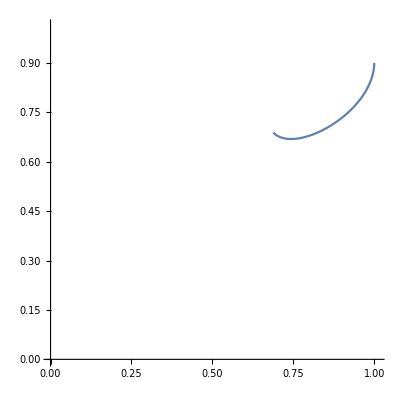

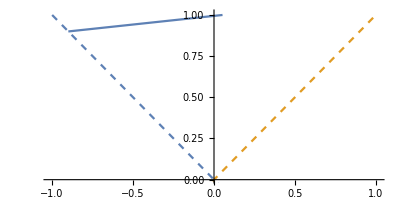

```mathematica
s=.9;
n=2;
m=1;
q1=Sin[1/2 ArcCos[(1-(1+s^n)t)/s^(n-m)]+1/2 ArcCos[(1-(1-s^n)t)/s^(n-m)]];
q2=Sin[1/2 ArcCos[(1-(1+s^n)t)/s^(n-m)]-1/2 ArcCos[(1-(1-s^n)t)/s^(n-m)]];
ParametricPlot[{q1,q2},{t,(1-s^(n-m))/(1-s^n),1},PlotRange->{{0,1.01},{0,1.01}}]
x=(1-(1+s^n)t)/s^(n-m);
y=(1-(1-s^n)t)/s^(n-m);
Show[ParametricPlot[{x,y},{t,(1-s^(n-m))/(1-s^n),1},PlotRange->{{-1.01,1.01},{0,1.01}}],
Plot[{-x,x},{x,-1,1},PlotStyle->Dashed]]

Clear[q1,q2,n,m,s,x,y]
```

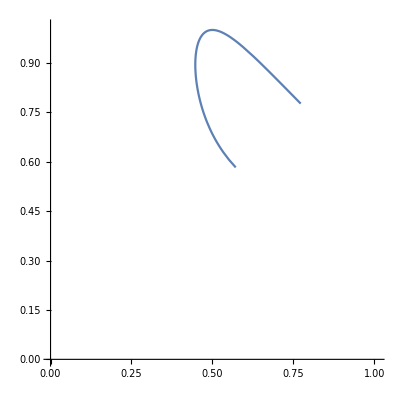

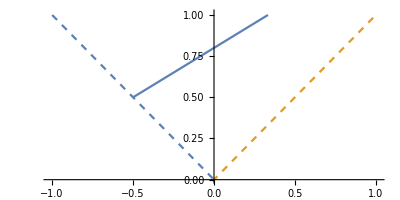

```mathematica
s=.5;
n=2;
m=1;
q1=Sin[1/2 ArcSin[(1-(1-s^n)t)/s^-m]+1/2 ArcSin[(1+(1+s^n)t)/s^-m]];
q2=Cos[1/2 ArcSin[(1-(1-s^n)t)/s^-m]-1/2 ArcSin[(1+(1+s^n)t)/s^-m]];
ParametricPlot[{q1,q2},{t,-10,10},PlotRange->{{0,1.01},{0,1.01}}]
x=(1-(1+s^n)t)/s^(n-m);
y=(1-(1-s^n)t)/s^(n-m);
Show[ParametricPlot[{x,y},{t,(1-s^(n-m))/(1-s^n),1},PlotRange->{{-1.01,1.01},{0,1.01}}],
Plot[{-x,x},{x,-1,1},PlotStyle->Dashed]]

Clear[q1,q2,n,m,s,x,y]
```

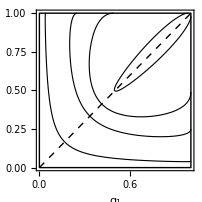

```mathematica
m=1;n=2;
s=.2;

Show[Table[Show[ParametricPlot[{Sin[1/2 ArcCos[(1-(1+s^n)t)/s^(n-m)]+1/2 ArcCos[(1-(1-s^n)t)/s^(n-m)]]^2,Sin[1/2 ArcCos[(1-(1+s^n)t)/s^(n-m)]-1/2 ArcCos[(1-(1-s^n)t)/s^(n-m)]]^2},{t,(1-s^(n-m))/(1-s^n),Min[1/(1-s^n),(1+s^(n-m))/(1+s^n),1]},PlotRange->{{0,1},{0,1}},
PlotStyle->Directive[Thickness[.004],Black],
Frame->True,FrameLabel->{Subscript[q, 1],Subscript[q, 2]},FrameStyle->Directive[Black,FontSize->9,FontFamily->"Times"]],ParametricPlot[{Sin[1/2 ArcCos[(1-(1+s^n)t)/s^(n-m)]-1/2 ArcCos[(1-(1-s^n)t)/s^(n-m)]]^2,Sin[1/2 ArcCos[(1-(1+s^n)t)/s^(n-m)]+1/2 ArcCos[(1-(1-s^n)t)/s^(n-m)]]^2},{t,(1-s^(n-m))/(1-s^n),Min[1/(1-s^n),(1+s^(n-m))/(1+s^n),1]},PlotRange->{{0,1},{0,1}},
PlotStyle->Directive[Thickness[.004],Black],
Frame->True,FrameLabel->{Subscript[q, 1],Subscript[q, 2]},FrameStyle->Directive[Black,FontSize->9,FontFamily->"Times"]]],{s,{0.2,0.5,0.7,.99}}],Graphics[Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}]],Graphics[{Dashed,Line[{{0,0},{1,1}}]}]]


Clear[s,m,n]
```

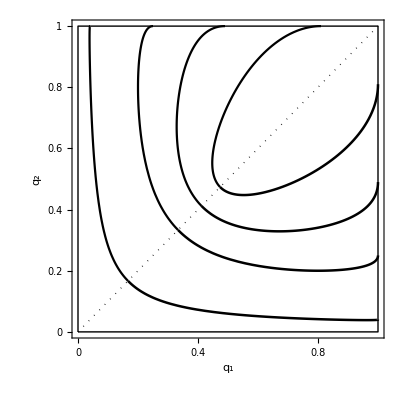

```mathematica
m=1;n=2;
s=.2;

ll=Show[Table[Show[ParametricPlot[{Sin[1/2 ArcCos[(1-(1+s^n)t)/s^(n-m)]+1/2 ArcCos[(1-(1-s^n)t)/s^(n-m)]]^2,Sin[1/2 ArcCos[(1-(1+s^n)t)/s^(n-m)]-1/2 ArcCos[(1-(1-s^n)t)/s^(n-m)]]^2},{t,(1-s^(n-m))/(1-s^n),Min[1/(1-s^n),(1+s^(n-m))/(1+s^n),1]},PlotRange->{{0,1},{0,1}},AspectRatio-> 1,PlotStyle->Directive[Thickness[.0045],Black],FrameTicks->{{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}},{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}}},FrameTicksStyle->{{Black,Black},{Black,Black}},
Frame->True,FrameLabel->{Subscript[q, 1],Subscript[q, 2]},FrameStyle->Directive[Black,FontSize->18,FontFamily->"Times"]],ParametricPlot[{Sin[1/2 ArcCos[(1-(1+s^n)t)/s^(n-m)]-1/2 ArcCos[(1-(1-s^n)t)/s^(n-m)]]^2,Sin[1/2 ArcCos[(1-(1+s^n)t)/s^(n-m)]+1/2 ArcCos[(1-(1-s^n)t)/s^(n-m)]]^2},{t,(1-s^(n-m))/(1-s^n),Min[1/(1-s^n),(1+s^(n-m))/(1+s^n),1]},PlotRange->{{0,1},{0,1}},
PlotStyle->Directive[Thickness[.004],Black],
Frame->True,FrameLabel->{Subscript[q, 1],Subscript[q, 2]},FrameStyle->Directive[Black,FontSize->9,FontFamily->"Times"]]],{s,set={0.2,0.5,0.7,.9}}],Graphics[Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}]],Graphics[{Dotted,Line[{{0,0},{1,1}}]}]]


Clear[s,m,n]
```

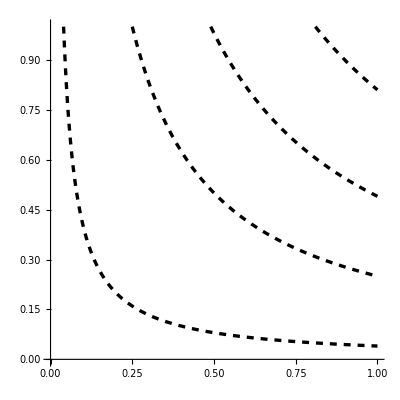

```mathematica
m=1;n=5;
s=.2;

kk=Show[Table[Plot[s^(2m)/q1,{q1,s^(2m),1},PlotRange->{{0,1},{0,1}},AspectRatio->1,PlotStyle->Directive[Thickness[.006],Black,Dashed]],{s,set}]]


Clear[s,m,n]
```

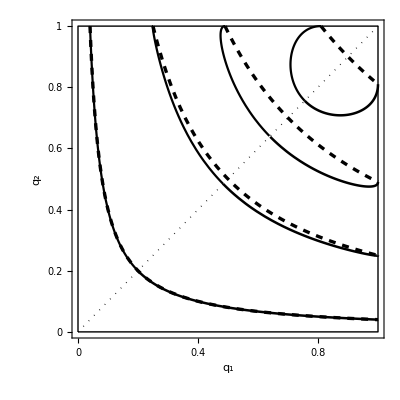

```mathematica
Show[ll,kk]
```

```mathematica
0.65/0.85 36
```

27.5294

```mathematica
(q2p q1-q1p q2)/(q2p-q1p)q1^2/q1^2=(q2p q1-q1p q2)/(q2p-q1p)q1^2/q1^2==(d/dt(q2/q1))/(q2p-q1p)q1^2
```

```mathematica
Clear[x,y]
```

```mathematica
((√(q2(1-q2)))/s^(n-m)((1+s^n)/(√(1-x^2))-(1-s^n)/(√(1-y^2))))/((√(q2(1-q2)))/s^(n-m)((1+s^n)/(√(1-x^2))-(1-s^n)/(√(1-y^2)))-(√(q1(1-q1)))/s^(n-m)((1+s^n)/(√(1-x^2))+(1-s^n)/(√(1-y^2))))
```

(√((1-q2) q2) s^(m-n) ((1+s^n)/(√(1-x^2))-(1-s^n)/(√(1-y^2))))/(√((1-q2) q2) s^(m-n) ((1+s^n)/(√(1-x^2))-(1-s^n)/(√(1-y^2)))-√((1-q1) q1) s^(m-n) ((1+s^n)/(√(1-x^2))+(1-s^n)/(√(1-y^2))))

```mathematica
(√(q2(1-q2))((1+s^n)/(√(1-x^2))-(1-s^n)/(√(1-y^2))))/(√(q2(1-q2))((1+s^n)/(√(1-x^2))-(1-s^n)/(√(1-y^2)))-√(q1(1-q1))((1+s^n)/(√(1-x^2))+(1-s^n)/(√(1-y^2))))
```

```mathematica
1-(√(q1(1-q1))((1+s^n)/(√(1-x^2))+(1-s^n)/(√(1-y^2))))/(√(q2(1-q2))((1+s^n)/(√(1-x^2))-(1-s^n)/(√(1-y^2))))=1/η1
```

```mathematica
(q1-(√(q1(1-q1))((1+s^n)/(√(1-x^2))+(1-s^n)/(√(1-y^2))))/(√(q2(1-q2))((1+s^n)/(√(1-x^2))-(1-s^n)/(√(1-y^2))))q2)/(1-(√(q1(1-q1))((1+s^n)/(√(1-x^2))+(1-s^n)/(√(1-y^2))))/(√(q2(1-q2))((1+s^n)/(√(1-x^2))-(1-s^n)/(√(1-y^2)))))
```

```mathematica
(q1+(1/η1-1)q2)/(1/η1)
```

```mathematica
t
```

6.92526

{0.249999,0.499511}

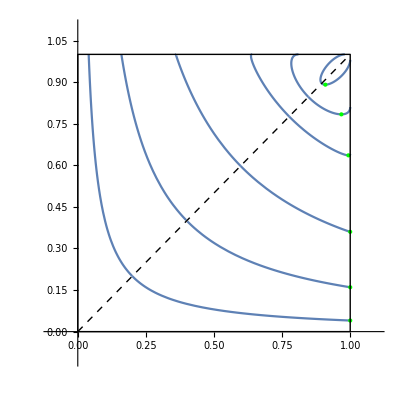

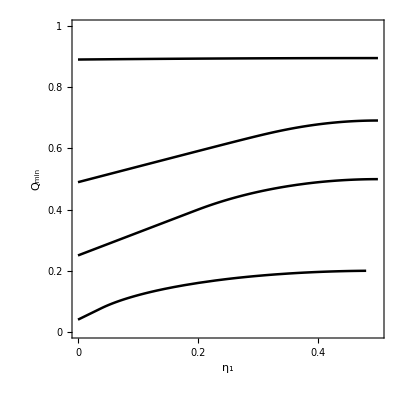

```mathematica
m=1;n=10;Clear[t]
s=.5;
{(s^(2m)-s^(2n))/(1-s^(2n)),(s^m-s^n)/(1-s^n)}

x=(1-(1+s^n)t)/s^(n-m);
y=(1-(1-s^n)t)/s^(n-m);

Show[Table[x=(1-(1+s^n)t)/s^(n-m);y=(1-(1-s^n)t)/s^(n-m);q1=(1-x y+√(1-x^2)√(1-y^2))/2;q2=(1-x y-√(1-x^2)√(1-y^2))/2;Show[ParametricPlot[{q1,q2},{t,(1-s^(n-m))/(1-s^n),1},PlotRange->{{-0.1,1.1},{-.1,1.1}}],ParametricPlot[{q2,q1},{t,(1-s^(n-m))/(1-s^n),1},PlotRange->{{-0.1,1.1},{-.1,1.1}}],Graphics[{Green,Point[{(1-s^(2 n-2m))/(1-s^(2 n)),(s^(2 m)-s^(2 n))/(1-s^(2 n))}]}]],{s,{0.2,0.4,0.6,0.8,.9,.99}}],Graphics[Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}]],Graphics[{Dashed,Line[{{0,0},{1,1}}]}]]

(**********************************************************************************************************************************)

(*Show[Table[x=(1-(1+s^n)t)/s^(n-m);y=(1-(1-s^n)t)/s^(n-m);q1=(1-x y+√(1-x^2)√(1-y^2))/2;q2=(1-x y-√(1-x^2)√(1-y^2))/2;
dq1=(√(q1(1-q1)))/s^(n-m)((1+s^n)/(√(1-x^2))+(1-s^n)/(√(1-y^2)));dq2=(√(q2(1-q2)))/s^(n-m)((1+s^n)/(√(1-x^2))-(1-s^n)/(√(1-y^2)));ParametricPlot[{dq2/(dq2-dq1),dq2/(dq2-dq1)q1+dq1/(dq1-dq2)q2},{t,(1-s^(n-m))/(1-s^n)+10^-10,(1-s^(2 n-2m))/(1-s^(2 n))},PlotRange->{{-0.1,.6},{-.1,.6}}],{s,{0.2,0.4,0.6,0.8,.9,.99}}]]*)


Uf=Show[Table[x=(1-(1+s^n)t)/s^(n-m);y=(1-(1-s^n)t)/s^(n-m);q1=(1-x y+√(1-x^2)√(1-y^2))/2;q2=(1-x y-√(1-x^2)√(1-y^2))/2;
dq1=(√(q1(1-q1)))/s^(n-m)((1+s^n)/(√(1-x^2))+(1-s^n)/(√(1-y^2)));dq2=(√(q2(1-q2)))/s^(n-m)((1+s^n)/(√(1-x^2))-(1-s^n)/(√(1-y^2)));ParametricPlot[{dq2/(dq2-dq1),(dq2 q1-dq1 q2)/(dq2-dq1)},{t,(1-s^(n-m))/(1-s^n)+10^-10,(1-s^(2 n-2m))/(1-s^(2 n))},PlotRange->{{0,.5},{0,1}},AspectRatio-> 1,PlotStyle->Directive[Thickness[.0045],Black],FrameTicks->{{{0,0.2,0.4,0.6,0.8,1},{0.2,0.4,0.6,0.8,1}},{{0,0.1,0.2,0.3,0.4,0.5},{0.1,0.2,0.3,0.4}}},FrameTicksStyle->{{Black,Black},{Black,Black}},
Frame->True,FrameLabel->{Subscript[η, 1],Subscript[Q, min]},FrameStyle->Directive[Black,FontSize->18,FontFamily->"Times"]],{s,{0.2,0.5,0.7,.99}}]]

UD=Table[Plot[If[η1≤s^(2m)/(1+s^(2m)),η1+s^(2m)(1-η1),2 √(η1(1-η1))s^m],{η1,0,1/2},AspectRatio-> 1,PlotStyle->Directive[Thickness[.006],Black,Dashed]],{s,{0.2,.5,.7,.99}}];




Clear[s,m,n]
```

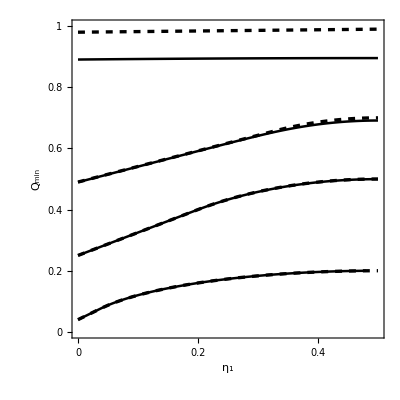

```mathematica
Show[Uf,UD]
```

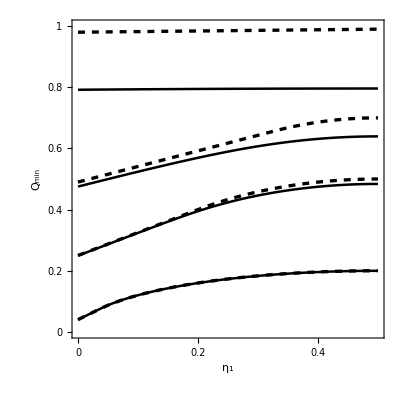

```mathematica
Show[Uf,UD]
```

```mathematica
FullSimplify[{η1+s^(2m)(1-η1),2 √(η1(1-η1))s^m}/. η1->s^(2m)/(1+s^(2m))//FullSimplify,{n>0,m>0,s>0}]
```

{2-2/(1+s^(2 m)),2-2/(1+s^(2 m))}

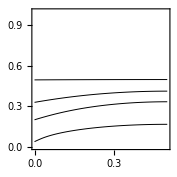
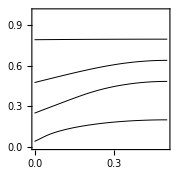

```mathematica
s=.5;m=1;
s^(2m)

n=10;
ja=Table[{n,q1/.NMinimize[{Abs[dq2/dq1+.9],(1-s^(n-m))/(1-s^n)≤ t≤(1-s^(2 n-2m))/(1-s^(2 n)) },t][[2]]},{n,2,20}]

Clear[s,n,m]
```

0.25

{{2,0.345349},{3,0.44711},{4,0.4891},{5,0.508502},{6,0.517872},{7,0.522482},{8,0.52477},{9,0.52591},{10,0.526478},{11,0.52676},{12,0.526904},{13,0.526975},{14,0.527011},{15,0.527029},{16,0.527037},{17,0.527042},{18,0.527044},{19,0.527045},{20,0.527046}}

```mathematica
Show[Plot[1,{n,0,20}],ListPlot[ja,PlotMarkers->"◦"]]
```

-Graphics-

0.25

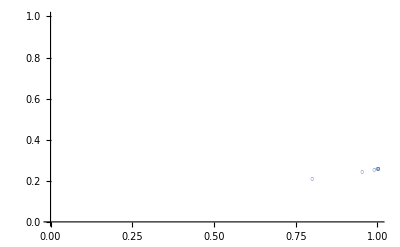
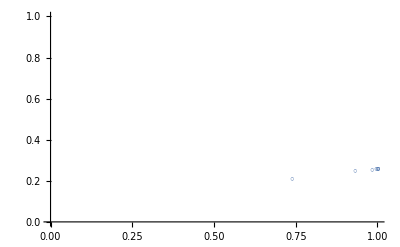
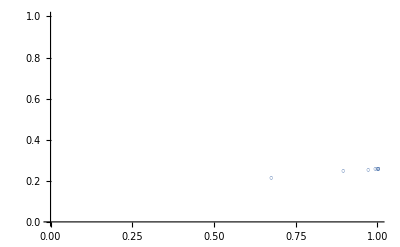
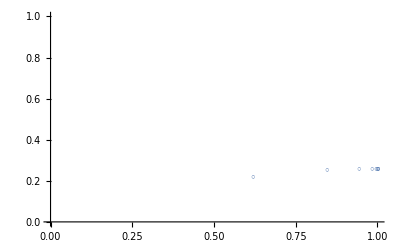
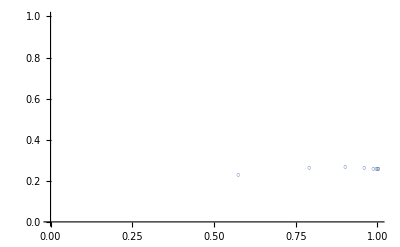
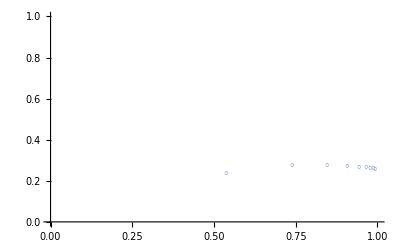
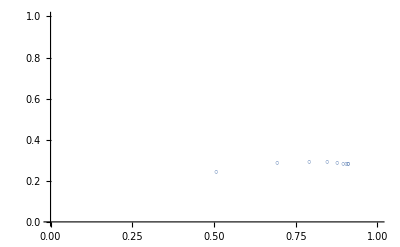
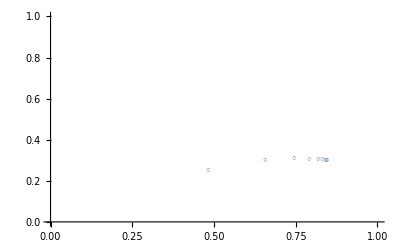

```mathematica
s=.5;m=1;
s^(2m)

n=10;
ja=Table[ListPlot[Table[{q1/.(çç=NMinimize[{Abs[dq2/dq1+a],(1-s^(n-m))/(1-s^n)≤ t≤(1-s^(2 n-2m))/(1-s^(2 n)) },t][[2]]),q2/.çç},{n,2,10}],PlotRange->{{0,1},{0,1}},PlotMarkers->"◦"],{a,0,.99,.05}]

Clear[s,n,m]
```

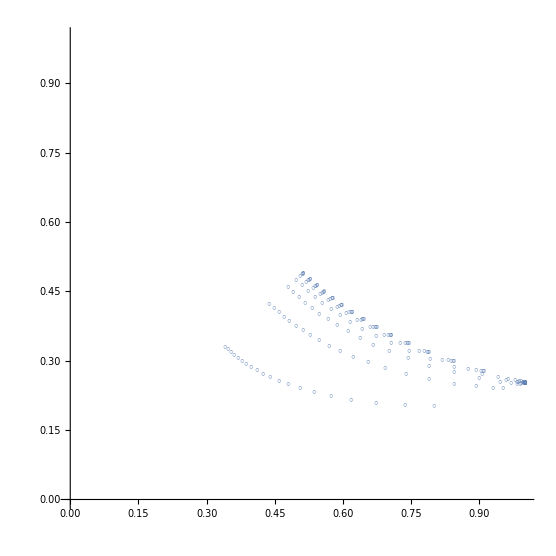

```mathematica
Show[ja,AspectRatio->1]
```

```mathematica
s=.5;m=1;
s^(2m)

n=10;
ja=ListPlot[Table[Table[{q1/.(çç=NMinimize[{Abs[dq2/dq1+a],(1-s^(n-m))/(1-s^n)≤ t≤(1-s^(2 n-2m))/(1-s^(2 n)) },t][[2]]),q2/.çç},{n,2,30}],{a,0,.24,.02}],PlotRange->{{.5,1},{0,.5}},PlotMarkers->"◦"]

Clear[s,n,m]
```

0.25

NMinimize::nnum: The function value Indeterminate is not a number at {t} = {1.}.

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMinimize :: cvmit will be suppressed during this calculation.

NMinimize::nnum: The function value Indeterminate is not a number at {t} = {1.}.

General::stop: Further output of NMinimize :: nnum will be suppressed during this calculation.

-Graphics-

```mathematica
s=.5;m=1;
s^(2m)

n=10;
ja=ListPlot[Table[Table[{q1/.(çç=NMinimize[{Abs[dq2/dq1+a],(1-s^(n-m))/(1-s^n)≤ t≤(1-s^(2 n-2m))/(1-s^(2 n)) },t][[2]]),q2/.çç},{n,2,30}],{a,.26,.5,.02}],PlotRange->{{.5,1},{0,.5}},PlotMarkers->"◦"]

Clear[s,n,m]
```

0.25

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

-Graphics-

```mathematica
popo=D[If[η1≤s^(2m)/(1+s^(2m)),η1+s^(2m)(1-η1),2 √(η1(1-η1))s^m],{η1,1}]//Simplify
```

Piecewise[{{1-s^(2 m), s^(2 m)/(1+s^(2 m))≥η1}, {(s^m (1-2 η1))/(√(-(-1+η1) η1)), True}}]

```mathematica
pupu=D[If[η1≤s^(2m)/(1+s^(2m)),η1+s^(2m)(1-η1),2 √(η1(1-η1))s^m],{η1,2}]//Simplify
```

Piecewise[{{-s^m/(2 (-(-1+η1) η1)^(3/2)), s^(2 m)/(1+s^(2 m))<η1}, {0, True}}]

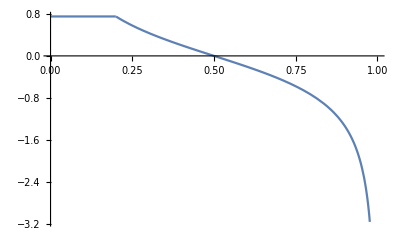

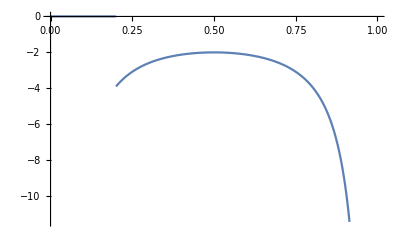

-Graphics-

```mathematica
s=.5;
m=1;
Plot[popo,{η1,0,1}]
Plot[pupu,{η1,0,1}]
Clear[s,m]
```

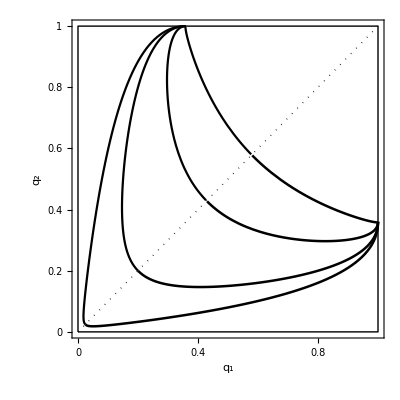

```mathematica
m=1;
s=.6;

ll=Show[Table[n=Log[sp]/Log[s];Show[ParametricPlot[{Sin[1/2 ArcCos[(1-(1+s^n)t)/s^(n-m)]+1/2 ArcCos[(1-(1-s^n)t)/s^(n-m)]]^2,Sin[1/2 ArcCos[(1-(1+s^n)t)/s^(n-m)]-1/2 ArcCos[(1-(1-s^n)t)/s^(n-m)]]^2},{t,(1-s^(n-m))/(1-s^n),Min[1/(1-s^n),(1+s^(n-m))/(1+s^n),1]},PlotRange->{{0,1},{0,1}},AspectRatio-> 1,PlotStyle->Directive[Thickness[.0045],Black],FrameTicks->{{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}},{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}}},FrameTicksStyle->{{Black,Black},{Black,Black}},
Frame->True,FrameLabel->{Subscript[q, 1],Subscript[q, 2]},FrameStyle->Directive[Black,FontSize->18,FontFamily->"Times"]],ParametricPlot[{Sin[1/2 ArcCos[(1-(1+s^n)t)/s^(n-m)]-1/2 ArcCos[(1-(1-s^n)t)/s^(n-m)]]^2,Sin[1/2 ArcCos[(1-(1+s^n)t)/s^(n-m)]+1/2 ArcCos[(1-(1-s^n)t)/s^(n-m)]]^2},{t,(1-s^(n-m))/(1-s^n),Min[1/(1-s^n),(1+s^(n-m))/(1+s^n),1]},PlotRange->{{0,1},{0,1}},
PlotStyle->Directive[Thickness[.004],Black],
Frame->True,FrameLabel->{Subscript[q, 1],Subscript[q, 2]},FrameStyle->Directive[Black,FontSize->9,FontFamily->"Times"]]],{sp,set={0.05,0.3,0.5,.59}}],Graphics[Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}]],Graphics[{Dotted,Line[{{0,0},{1,1}}]}]]


Clear[s,m,n]
```

{(0.36-0.6^(2 n))/(1-0.6^(2 n)),(0.6-0.6^n)/(1-0.6^n)}

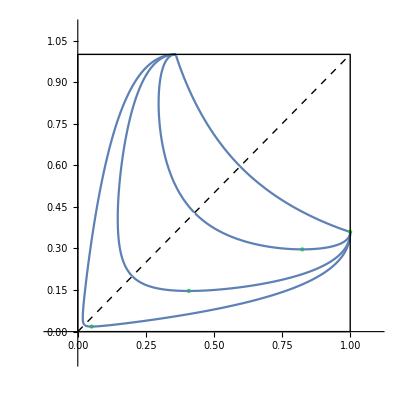

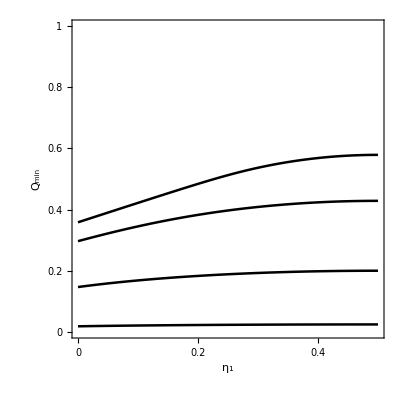

```mathematica
m=1;Clear[t]
s=.6;
{(s^(2m)-s^(2n))/(1-s^(2n)),(s^m-s^n)/(1-s^n)}

x=(1-(1+s^n)t)/s^(n-m);
y=(1-(1-s^n)t)/s^(n-m);

Show[Table[n=Log[sp]/Log[s];x=(1-(1+s^n)t)/s^(n-m);y=(1-(1-s^n)t)/s^(n-m);q1=(1-x y+√(1-x^2)√(1-y^2))/2;q2=(1-x y-√(1-x^2)√(1-y^2))/2;Show[ParametricPlot[{q1,q2},{t,(1-s^(n-m))/(1-s^n),1},PlotRange->{{-0.1,1.1},{-.1,1.1}}],ParametricPlot[{q2,q1},{t,(1-s^(n-m))/(1-s^n),1},PlotRange->{{-0.1,1.1},{-.1,1.1}}],Graphics[{Green,Point[{(1-s^(2 n-2m))/(1-s^(2 n)),(s^(2 m)-s^(2 n))/(1-s^(2 n))}]}]],{sp,{0.01,0.3,0.5,.59}}],Graphics[Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}]],Graphics[{Dashed,Line[{{0,0},{1,1}}]}]]

(**********************************************************************************************************************************)

(*Show[Table[x=(1-(1+s^n)t)/s^(n-m);y=(1-(1-s^n)t)/s^(n-m);q1=(1-x y+√(1-x^2)√(1-y^2))/2;q2=(1-x y-√(1-x^2)√(1-y^2))/2;
dq1=(√(q1(1-q1)))/s^(n-m)((1+s^n)/(√(1-x^2))+(1-s^n)/(√(1-y^2)));dq2=(√(q2(1-q2)))/s^(n-m)((1+s^n)/(√(1-x^2))-(1-s^n)/(√(1-y^2)));ParametricPlot[{dq2/(dq2-dq1),dq2/(dq2-dq1)q1+dq1/(dq1-dq2)q2},{t,(1-s^(n-m))/(1-s^n)+10^-10,(1-s^(2 n-2m))/(1-s^(2 n))},PlotRange->{{-0.1,.6},{-.1,.6}}],{s,{0.2,0.4,0.6,0.8,.9,.99}}]]*)


Uf=Show[Table[n=Log[sp]/Log[s];x=(1-(1+s^n)t)/s^(n-m);y=(1-(1-s^n)t)/s^(n-m);q1=(1-x y+√(1-x^2)√(1-y^2))/2;q2=(1-x y-√(1-x^2)√(1-y^2))/2;
dq1=(√(q1(1-q1)))/s^(n-m)((1+s^n)/(√(1-x^2))+(1-s^n)/(√(1-y^2)));dq2=(√(q2(1-q2)))/s^(n-m)((1+s^n)/(√(1-x^2))-(1-s^n)/(√(1-y^2)));ParametricPlot[{dq2/(dq2-dq1),(dq2 q1-dq1 q2)/(dq2-dq1)},{t,(1-s^(n-m))/(1-s^n)+10^-10,(1-s^(2 n-2m))/(1-s^(2 n))},PlotRange->{{0,.5},{0,1}},AspectRatio-> 1,PlotStyle->Directive[Thickness[.0045],Black],FrameTicks->{{{0,0.2,0.4,0.6,0.8,1},{0.2,0.4,0.6,0.8,1}},{{0,0.1,0.2,0.3,0.4,0.5},{0.1,0.2,0.3,0.4}}},FrameTicksStyle->{{Black,Black},{Black,Black}},
Frame->True,FrameLabel->{Subscript[η, 1],Subscript[Q, min]},FrameStyle->Directive[Black,FontSize->18,FontFamily->"Times"]],{sp,{0.05,0.3,0.5,.59}}]]

UD=Plot[If[η1≤s^(2m)/(1+s^(2m)),η1+s^(2m)(1-η1),2 √(η1(1-η1))s^m],{η1,0,1/2},AspectRatio-> 1,PlotStyle->Directive[Thickness[.006],Black,Dashed]];




Clear[s,m,n]
```

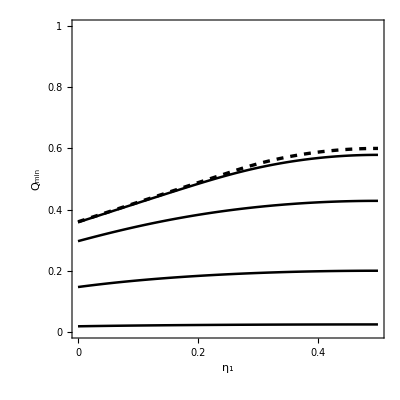

```mathematica
Show[Uf,UD]
```

## NEWER

{0.666667,1}

-Graphics-

{0.857143,1}

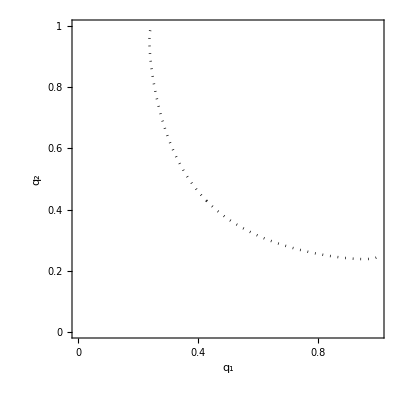

-Graphics-

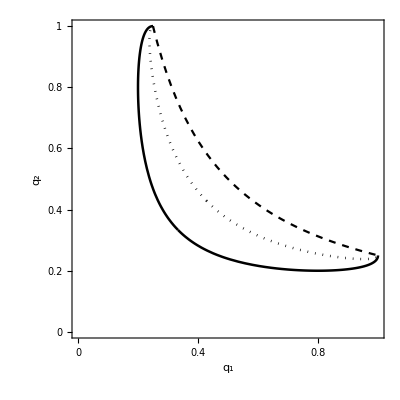

```mathematica
s=0.5;
sp=s^2;
α=1;
ϕ=1;
β=π/6;
x=(1-(ϕ+α sp)t)/(α sp/s);
y=(1-(ϕ-α sp)t)/(α sp/s);q1=(1-x y+√(1-x^2)√(1-y^2))/2;q2=(1-x y-√(1-x^2)√(1-y^2))/2;
{(1-α sp/s)/(ϕ-α sp),1/ϕ}
out=Show[
ParametricPlot[{q1,q2},{t,(1-α sp/s)/(ϕ-α  sp),1/ϕ},PlotRange->{{0,1},{0,1}}
,AspectRatio-> 1,PlotStyle->Directive[Thickness[.0045],Black],FrameTicks->{{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}},{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}}},FrameTicksStyle->{{Black,Black},{Black,Black}},
Frame->True,FrameLabel->{Subscript[q, 1],Subscript[q, 2]},FrameStyle->Directive[Black,FontSize->18,FontFamily->"Times"]
],
ParametricPlot[{q2,q1},{t,(1-α sp/s)/(ϕ-α sp),1/ϕ},PlotRange->{{0,1},{0,1}},AspectRatio-> 1,PlotStyle->Directive[Thickness[.0045],Black],FrameTicks->{{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}},{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}}},FrameTicksStyle->{{Black,Black},{Black,Black}},
Frame->True,FrameLabel->{Subscript[q, 1],Subscript[q, 2]},FrameStyle->Directive[Black,FontSize->18,FontFamily->"Times"]
]
]
Clear[α]
α=.5;

x=(1-(ϕ+α sp)t)/(α sp/s);
y=(1-(ϕ-α sp)t)/(α sp/s);q1=(1-x y+√(1-x^2)√(1-y^2))/2;q2=(1-x y-√(1-x^2)√(1-y^2))/2;
{(1-α sp/s)/(ϕ-α sp),1/ϕ}
in=Show[
ParametricPlot[{q1,q2},{t,(1-α sp/s)/(ϕ-α  sp),1/ϕ},PlotRange->{{0,1},{0,1}}
,AspectRatio-> 1,PlotStyle->Directive[Thickness[.0045],Black,Dotted],FrameTicks->{{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}},{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}}},FrameTicksStyle->{{Black,Black},{Black,Black}},
Frame->True,FrameLabel->{Subscript[q, 1],Subscript[q, 2]},FrameStyle->Directive[Black,FontSize->18,FontFamily->"Times"]
],
ParametricPlot[{q2,q1},{t,(1-α sp/s)/(ϕ-α sp),1/ϕ},PlotRange->{{0,1},{0,1}},AspectRatio-> 1,PlotStyle->Directive[Thickness[.0045],Black,Dotted],FrameTicks->{{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}},{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}}},FrameTicksStyle->{{Black,Black},{Black,Black}},
Frame->True,FrameLabel->{Subscript[q, 1],Subscript[q, 2]},FrameStyle->Directive[Black,FontSize->18,FontFamily->"Times"]
]
]

SUS={t->1/(2 (sp α-ϕ) (sp α+ϕ))Csc[β] Sec[β] (-2 s ϕ √(Cos[β] Sin[β])+sp^2 α^2 (Cos[β]+Sin[β])-sp α √(sp^2 α^2-4 s ϕ √(Cos[β] Sin[β]) (Cos[β]+Sin[β])+(2 s^2-sp^2 α^2+2 ϕ^2) Sin[2 β])),t->1/(2 (sp α-ϕ) (sp α+ϕ))(-2 s ϕ √(Csc[β] Sec[β])+sp α Csc[β] Sec[β] (sp α (Cos[β]+Sin[β])+√(sp^2 α^2-4 s ϕ √(Cos[β] Sin[β]) (Cos[β]+Sin[β])+(2 s^2-sp^2 α^2+2 ϕ^2) Sin[2 β])))};

Clear[t]
ppp1=Graphics[{Black,PointSize->Medium,Point[{Cos[β]t,Sin[β]t}/. SUS[[1]]]}];
ppp2=Graphics[{Black,PointSize->Medium,Point[{Cos[β]t,Sin[β]t}/. SUS[[2]]]}];
lll=ParametricPlot[{Cos[β]t,Sin[β]t},{t,0,Max[t/. SUS[[1]],t/. SUS[[2]]]}];
asy=Plot[s^2/(ϕ^2 q1),{q1,s^2/ϕ^2,1},PlotStyle->Directive[Thickness[.004],Black,Dashed]]


SA1=Show[in,out,asy]
```